```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Definiciones de

```mathematica
cSpeed=137.035999139;
nm=100./5.2918;
wp=0.48297106037599996;
gam=0.007244389509;
```

```mathematica
ϵDrude[ω_,ωp_,γ_]=1-ωp^2/(ω(ω+ⅈ γ));
```

```mathematica
II[l_,m_,i1_,i2_]:=If[l==m-2 || l==m-1,
0.,
If[l==m,
If[Mod[i2,2]==0,(-1.)^m Factorial2[2m-1]Beta[(i1+m+2)/2,(i2+1)/2],0],
1./(l-m)((2l-1)*II[l-1,m,i1,i2+1]-(l+m-1)II[l-2,m,i1,i2])
]
]
```

```mathematica
IM[l1_,l2_,m1_,m2_]:=NIntegrate[LegendreP[l1,m1,x]*LegendreP[l2,m2,x]*x,{x,-1,1}]
IU[l1_,l2_,m1_,m2_]:=NIntegrate[LegendreP[l1,m1,x]*LegendreP[l2,m2,x]*1/(√(1-x^2)),{x,-1,1}]
IV[l1_,l2_,m1_,m2_]:=NIntegrate[LegendreP[l1,m1,x]*LegendreP[l2,m2,x]*x^2/(√(1-x^2)),{x,-1,1}]
IW[l1_,l2_,m1_,m2_]:=NIntegrate[LegendreP[l1,m1,x]*LegendreP[l2,m2,x]*x/(√(1-x^2)),{x,-1,1}]
```

```mathematica
llmax=11;
Timing[IMlist=Table[IM[l1,l2,m1,m2],{l1,1,llmax},{l2,1,llmax},{m1,-l1,l1},{m2,-l2,l2}];
IUlist=Table[IU[l1,l2,m1,m2],{l1,1,llmax},{l2,1,llmax},{m1,-l1,l1},{m2,-l2,l2}];
IVlist=Table[IV[l1,l2,m1,m2],{l1,1,llmax},{l2,1,llmax},{m1,-l1,l1},{m2,-l2,l2}];
IWlist=Table[IW[l1,l2,m1,m2],{l1,1,llmax},{l2,1,llmax},{m1,-l1,l1},{m2,-l2,l2}];
]//Quiet
```

{988.781,Null}

```mathematica
Export["Integrals/IMlist.mx",IMlist];
Export["Integrals/IUlist.mx",IUlist];
Export["Integrals/IVlist.mx",IVlist];
Export["Integrals/IWlist.mx",IWlist];
```

```mathematica
llmax=11;
Timing[IIlist=Table[II[l,m,j, l-j],{l,1,llmax},{m,0,l},{j,m,l}];
]//Quiet
```

{0.140625,Null}

```mathematica
Export["Integrals/IIlist.mx",IIlist];
```

```mathematica
αlm[l_,m_]=√((2l+1.)/(4π)((l-m)!)/((l+m)!));
gamma[betav_]=1./(√(1-betav^2));
AA[l_,m_,betav_]:=If[m<0,
(-1)^Abs[m] AA[l,Abs[m],betav],
1./betav^(l+1)∑_(j=m)^l (ⅈ^(l-j)Factorial2[2l+1]αlm[l,m])/(gamma[betav]^j 2^j Factorial[(j-m)/2]Factorial[(j+m)/2])IIlist[[l,m+1,j+1-m]]
](*II[l,m,j,l-j]*)
BB[l_,m_,betav_]:=AA[l,m+1,betav] √((l+m+1)(l-m))-AA[l,m-1,betav] √((l-m+1)(l+m))
```

```mathematica
IMlist=Import["Integrals/IMlist.mx"];
IUlist=Import["Integrals/IUlist.mx"];
IVlist=Import["Integrals/IVlist.mx"];
IWlist=Import["Integrals/IWlist.mx"];
IIlist=Import["Integrals/IIlist.mx"];
```

```mathematica
j[l_,z_]=SphericalBesselJ[l,z];
dj[l_,z_]=j[l,z]+0.5*z*(j[l-1,z]-j[l+1,z]-j[l,z]/z);
h[l_,z_]=ⅈ SphericalHankelH1[l,z];
dh[l_,z_]=h[l,z]+0.5*z*(h[l-1,z]-h[l+1,z]-h[l,z]/z);
```

```mathematica
z[i_,l_,w_,r_]:={h[l,w*r/cSpeed],j[l,w*r/cSpeed]}[[i+1]];
f[i_,l_,w_,r_]:={(l+1)h[l,w*r/cSpeed]/(w*r/cSpeed)-h[l+1,w*r/cSpeed],(l+1)j[l,w*r/cSpeed]/(w*r/cSpeed)-j[l+1,w*r/cSpeed]}[[i+1]];
```

```mathematica
tEl[a_,w_, ϵ_,l_]:=(-j[l,w a/cSpeed]*dj[l,w a√ϵ[w]/cSpeed]+ϵ[w]j[l,w a √ϵ[w]/cSpeed]*dj[l,w a/cSpeed])/(h[l,w a/cSpeed]*dj[l,w a√ϵ[w]/cSpeed]-ϵ[w]j[l,w a √ϵ[w]/cSpeed]*dh[l,w a/cSpeed])
tMl[a_,w_, ϵ_,l_]:=(j[l,w a√ϵ[w]/cSpeed]*dj[l,w a/cSpeed]-j[l,w a /cSpeed]*dj[l,w a√ϵ[w]/cSpeed])/(h[l,w a/cSpeed]*dj[l,w a√ϵ[w]/cSpeed]-j[l,w a √ϵ[w]/cSpeed]*dh[l,w a/cSpeed])
```

```mathematica
ψE[l_,m_,w_,b_,betav_]=(-2π ⅈ^(l-1)w)/(cSpeed^2 gamma[betav])*BB[l,m,betav]/(l(l+1))BesselK[m,(w*b)/(betav*cSpeed*gamma[betav])];
ψM[l_,m_,w_,b_,betav_]=(-4π ⅈ^(l-1)w*betav)/(cSpeed^2 gamma[betav])*(m*AA[l,m,betav])/(l(l+1))BesselK[m,(w*b)/(betav*cSpeed*gamma[betav])];
```

```mathematica
DE[l_,m_,w_,b_,betav_]=ⅈ^l*αlm[l,m]*ψE[l,m,w,b,betav];
CM[l_,m_,w_,b_,betav_]=ⅈ^l*αlm[l,m]*ψM[l,m,w,b,betav];
```

#### Pruebas de funciones

```mathematica
ll=1;mm=1;betavv=0.7;jj=mm;ii1=jj;ii2=ll-jj;
AA[ll,mm,betavv]
BB[ll,mm,betavv]
```

-1.00707

0.-2.82036 ⅈ

```mathematica
ll=3;mm=0;jj=2;
IIlist[[ll,mm+1,jj-mm+1]]
II[ll,mm,jj,ll-jj]
```

-0.114286

-0.114286

```mathematica
IVlist[[1,1,-1+1+1]]
```

{0.0981748,0.,-0.19635}

```mathematica
aa=1.0*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];ll=1;
tEl[aa,ww,ϵϵ,ll]
```

3.49214×10^-17+8.8282×10^-23 ⅈ

```mathematica
ϵDrude[1,wp,gam]
```

0.766751+0.00168975 ⅈ

```mathematica
ll1=1;ll2=1;mm1=-1;mm2=-1;
IVlist[[ll1,ll2,mm1+ll1+1,mm2+ll2+1]]
IV[ll1,ll2,mm1,mm2]
```

0.0981748

0.0981748

#### IErtx

```mathematica
ll1=1;mm1=-1;ll2=1;mm2=0;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
ⅈ*(mm1-mm2)*(-tEl[aa,ww,ϵϵ,ll1]*DE[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*f[0,ll2,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-tMl[aa,ww,ϵϵ,ll1]*CM[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*z[0,ll2,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
ⅈ*(mm1-mm2)*(-DE[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*f[1,ll2,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-CM[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*z[1,ll2,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
ⅈ*(mm1-mm2)*(-tEl[aa,ww,ϵϵ,ll1]*DE[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*f[0,ll2,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-tMl[aa,ww,ϵϵ,ll1]*CM[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*z[0,ll2,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
ⅈ*(mm1-mm2)*(-DE[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*f[1,ll2,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-CM[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*z[1,ll2,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
```

5.99178×10^-13-4.1775×10^-29 ⅈ

-5.3074×10^-13+0. ⅈ

3.98753×10^-13+1.00805×10^-18 ⅈ

-7.97506×10^-13+2.01611×10^-18 ⅈ

```mathematica
aa
```

18.8972

```mathematica
1i*(dm1-dm2)*(-tEl[l1-1]*DE[l1-1][m1+l1]*conj(tEl[l2-1]*DE[l2-1][m2+l2]*dz[0][l2-1])*(df[0][l1-1]/(k0*r))*dl2*(dl2+1.)*((dl1+1.)*IW1-(dl1-dm1+1.)*IU2)-tMl[l1-1]*CM[l1-1][m1+l1]*conj(tEl[l2-1]*DE[l2-1][m2+l2]*dz[0][l2-1])*(dz[0][l1-1]/(k0*r))*dm1*dl2*(dl2+1.)*IU1);
```

#### IErty

```mathematica
ll1=1;mm1=-1;ll2=1;mm2=0;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=0.00016350137266446518;ϵϵ[w_]=ϵDrude[w,wp,gam];
(-tEl[aa,ww,ϵϵ,ll1]*DE[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*f[0,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-tMl[aa,ww,ϵϵ,ll1]*CM[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*z[0,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
(-DE[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*f[1,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-CM[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*z[1,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
(-tEl[aa,ww,ϵϵ,ll1]*DE[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*f[0,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-tMl[aa,ww,ϵϵ,ll1]*CM[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*z[0,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
(-DE[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*f[1,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-CM[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*z[1,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
```

4.47722×10^-26+2.93481×10^-12 ⅈ

0.-2.5996×10^-12 ⅈ

-2.9753×10^-17+1.95312×10^-12 ⅈ

-5.9506×10^-17-3.90624×10^-12 ⅈ

```mathematica
(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-DE[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])-CM[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]]);
```

Part::pkspec1: The expression l1 cannot be used as a part specification.

Part::pkspec1: The expression 1+l1 cannot be used as a part specification.

Part::pkspec1: The expression l1 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

#### IHrty

```mathematica
IHrty[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[(-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

#### IErfy

```mathematica
ll1=1;mm1=1;ll2=1;mm2=0;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
-(mm1-mm2)*(tMl[aa,ww,ϵϵ,ll1]*CM[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*z[0,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IV[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IW[ll1+1,ll2,mm1,mm2])+tEl[aa,ww,ϵϵ,ll1]*DE[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*f[0,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IW[ll1,ll2,mm1,mm2])
-(mm1-mm2)*(CM[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*z[1,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IV[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IW[ll1+1,ll2,mm1,mm2])+DE[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*f[1,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IW[ll1,ll2,mm1,mm2])
-(mm1-mm2)*(tMl[aa,ww,ϵϵ,ll1]*CM[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*z[0,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IV[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IW[ll1+1,ll2,mm1,mm2])+tEl[aa,ww,ϵϵ,ll1]*DE[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*f[0,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IW[ll1,ll2,mm1,mm2])
-(mm1-mm2)*(CM[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*z[1,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IV[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IW[ll1+1,ll2,mm1,mm2])+DE[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*f[1,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IW[ll1,ll2,mm1,mm2])
```

3.02416×10^-18+3.30315×10^-13 ⅈ

```mathematica
-(m1-m2)*(tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(CM[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+DE[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]]);
```

Part::pkspec1: The expression l1 cannot be used as a part specification.

Part::pkspec1: The expression 1+l1 cannot be used as a part specification.

Part::pkspec1: The expression l1 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
IErfy[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[-(m1-m2)*(tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

#### IHrfy

```mathematica
IHrfy[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[-(m1-m2)*(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(-DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

#### Fields

```mathematica
IErty[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])-CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

```mathematica
IHrty[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[(-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

```mathematica
IErfy[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[-(m1-m2)*(tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

```mathematica
IHrfy[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[-(m1-m2)*(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(-DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

#### Rest

```mathematica
ClearAll[m1,m2]
```

```mathematica
dldwEy[w_,lmax_,a_,b_,r_,betav_, ϵ_]:=Sum[If[m1==m2+1||m2==m1+1,1/(4π)r^3(IErty[l1,l2,m1,m2,w,a, r,b, betav, ϵ]-IErfy[l1,l2,m1,m2,w,a, r,b, betav, ϵ]),0],{l1,1,lmax},{l2,1,lmax},{m1,-l1,l1},{m2,-l2,l2}]
dldwHy[w_,lmax_,a_,b_,r_,betav_, ϵ_]:=Sum[If[m1==m2+1||m2==m1+1,1/(4π)r^3(IHrty[l1,l2,m1,m2,w,a, r,b, betav, ϵ]-IHrfy[l1,l2,m1,m2,w,a, r,b, betav, ϵ]),0],{l1,1,lmax},{l2,1,lmax},{m1,-l1,l1},{m2,-l2,l2}]
```

```mathematica
dldwmmEy[w_,l1_,l2_,a_,b_,r_,betav_, ϵ_]:=1/(4π)*r^3*∑_(m1=-l1)^l1 (∑_(m2=-l2)^l2 If[m1==m2+1||m2==m1+1,(IErty[l1,l2,m1,m2,w,a, r,b, betav, ϵ]-IErfy[l1,l2,m1,m2,w,a, r,b, betav, ϵ]),0])
dldwmmHy[w_,l1_, l2_,a_,b_,r_,betav_, ϵ_]:=1/(4π)*r^3*∑_(m1=-l1)^l1 (∑_(m2=-l2)^l2 If[m1==m2+1||m2==m1+1,(IHrty[l1,l2,m1,m2,w,a, r,b, betav, ϵ]-IHrfy[l1,l2,m1,m2,w,a, r,b, betav, ϵ]),0])
```

```mathematica
llmax=1;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.05*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
dldwEy[ww,llmax,aa,bb,rr,betavv,ϵϵ]
dldwHy[ww,llmax,aa,bb,rr,betavv,ϵϵ]
```

-1.72859×10^-14

1.28246×10^-18

```mathematica
llmax=3;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
NIntegrate[ dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet
NIntegrate[ dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet
```

-1.2826×10^-6

-9.67489×10^-10

```mathematica
llmax=1;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
NIntegrate[ dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet
NIntegrate[ dldwmmEy[ω,llmax,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet
```

-1.26054×10^-6

-1.26054×10^-6

```mathematica
llmax=1;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
NIntegrate[ dldwmmEy[ω,llmax,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]+NIntegrate[ dldwmmEy[ω,llmax+1,llmax+1,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet
```

-1.27228×10^-6

```mathematica
llmax=1;betavv=0.5;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
NIntegrate[ dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet
```

-0.000110708

```mathematica
llmax=2;betavv=0.5;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
NIntegrate[ dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]+NIntegrate[ dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet
```

-0.00011593

```mathematica
ScientificForm[-0.000017789295078641313]
```

-1.77893×10^-5

```mathematica
DLDWY[[1,1]]
```

0.2

```mathematica
llmax=1;betavv=0.5;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
DLDWYH= ParallelTable[{ω,dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
DLDWYE= ParallelTable[{ω,dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
```

```mathematica
llmax=2;betavv=0.7;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
DLDWYH2= ParallelTable[{ω,dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
DLDWYE2= ParallelTable[{ω,dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
```

```mathematica
llmax=3;betavv=0.7;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
DLDWYH3= ParallelTable[{ω,dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
DLDWYE3= ParallelTable[{ω,dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
```

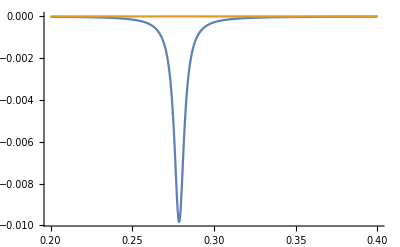

```mathematica
ListPlot[{DLDWYE, DLDWYH}, PlotRange->All, Joined->True, InterpolationOrder->2]
```

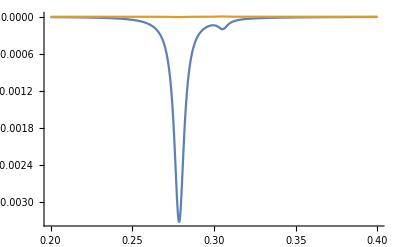

```mathematica
ListPlot[{DLDWYE2, DLDWYH2}, PlotRange->All, Joined->True, InterpolationOrder->2]
```

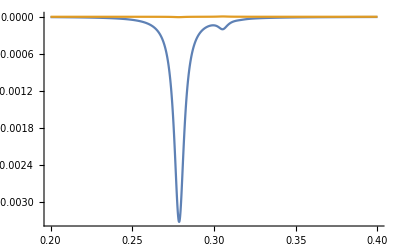

```mathematica
ListPlot[{DLDWYE3, DLDWYH3}, PlotRange->All, Joined->True, InterpolationOrder->2]
```

```mathematica
ll1=1;ll2=1;betavv=0.5;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
DLDWYMM1H= ParallelTable[{ω,dldwmmHy[ω,ll1,ll2,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
DLDWYMM1E= ParallelTable[{ω,dldwmmEy[ω,ll1,ll2,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
```

```mathematica
ll1=2;ll2=2;betavv=0.5;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
DLDWYMM2H= ParallelTable[{ω,dldwmmHy[ω,ll1,ll2,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
DLDWYMM2E= ParallelTable[{ω,dldwmmEy[ω,ll1,ll2,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
```

```mathematica
llmax=2;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
DLDWYH2= ParallelTable[{ω,dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
DLDWYE2= ParallelTable[{ω,dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
```

```mathematica
DLDWYMME;
```

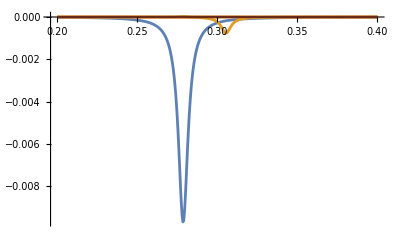

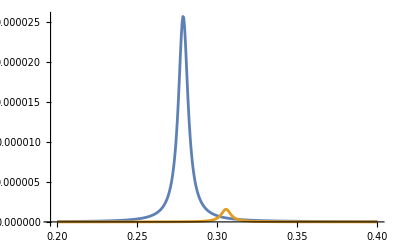

```mathematica
ListPlot[{DLDWYMM1E, DLDWYMM2E,DLDWYMM1H, DLDWYMM2H}, Joined->True, PlotRange->All]
ListPlot[{DLDWYMM1H, DLDWYMM2H}, Joined->True, PlotRange->All]
```

```mathematica
wp/√(5/2)
```

0.305458

```mathematica
Plot[]
```

$Aborted

```mathematica
IW[ll1,ll2,mm1,mm2]
IW[ll1+1,ll2,mm1,mm2]
IU[ll1,ll2,mm1,mm2]
IV[ll1,ll2,mm1,mm2]
```

0.333333

0.

0.

0.

```mathematica
dldwy[0]+=(1./(4.*Pi))*r*r*r*((IErty[2]-IErfy[2]).real()+(IErty[3]-IErfy[3]).real());
```

```mathematica
llmax=2;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
"l1=2  l2=1  m1=-2  m2=-1";
ll1=2;ll2=1;mm1=-1;mm2=-1;
IErfy[ll1,ll2,mm1,mm2,w,aa,rr,bb,betavv,ϵϵ]
```

0.

```mathematica
llmax=1;betavv=0.5;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
Lysmallb=ParallelTable[{b,NIntegrate[ dldwEy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet},{b,1,10}]
```

{{1,-0.00072021},{2,-0.00026825},{3,-0.000142794},{4,-0.0000880776},{5,-0.000058904},{6,-0.0000414595},{7,-0.0000302268},{8,-0.000022611},{9,-0.0000172484},{10,-0.0000133617}}

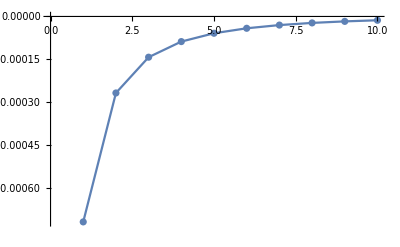

```mathematica
ListPlot[Lysmallb, Joined->True, Mesh->All]
```

```mathematica
llmax=1;betavv=0.6;aa=5.0*nm;bb=5.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];nn=10;
Lysmallb1=ParallelTable[{b,NIntegrate[ dldwEy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet},{b,5.5,10,(10-5.5)/nn}]
```

{{5.5,-0.00314431},{5.95,-0.00273219},{6.4,-0.00239122},{6.85,-0.00210584},{7.3,-0.00186458},{7.75,-0.00165885},{8.2,-0.00148207},{8.65,-0.00132913},{9.1,-0.00119601},{9.55,-0.00107951},{10.,-0.000977065}}

{{5.5,-0.00314431},{5.95,-0.00273219},{6.4,-0.00239122},{6.85,-0.00210584},{7.3,-0.00186458},{7.75,-0.00165885},{8.2,-0.00148207},{8.65,-0.00132913},{9.1,-0.00119601},{9.55,-0.00107951},{10.,-0.000977065}}

```mathematica
llmax=2;betavv=0.6;aa=5.0*nm;bb=5.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];nn=10;
Lysmallb2=ParallelTable[{b,NIntegrate[ dldwEy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet},{b,5.5,10,(10-5.5)/nn}]
```

{{5.5,-0.00561579},{5.95,-0.00468705},{6.4,-0.00396314},{6.85,-0.0033878},{7.3,-0.00292294},{7.75,-0.00254197},{8.2,-0.0022259},{8.65,-0.00196086},{9.1,-0.00173652},{9.55,-0.00154505},{10.,-0.00138042}}

```mathematica
llmax=3;betavv=0.6;aa=5.0*nm;bb=5.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];nn=10;
Lysmallb3=Table[{b,NIntegrate[ dldwEy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ],{ω,0, 40 }]},{b,5.5,10,(10-5.5)/nn}]//Quiet
```

NIntegrate::inumr: The integrand 0.+«9»+«87» has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,40}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{5.5,-0.00671678},{5.95,NIntegrate[dldwEy[ω,llmax,aa,b nm,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,b nm,rr,betavv,ϵϵ],{ω,0,40}]},{6.4,2.2786×10^78},{6.85,-0.00378171},{7.3,3.44766×10^60},{7.75,NIntegrate[dldwEy[ω,llmax,aa,b nm,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,b nm,rr,betavv,ϵϵ],{ω,0,40}]},{8.2,3.44743×10^60},{8.65,NIntegrate[dldwEy[ω,llmax,aa,b nm,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,b nm,rr,betavv,ϵϵ],{ω,0,40}]},{9.1,NIntegrate[dldwEy[ω,llmax,aa,b nm,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,b nm,rr,betavv,ϵϵ],{ω,0,40}]},{9.55,NIntegrate[dldwEy[ω,llmax,aa,b nm,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,b nm,rr,betavv,ϵϵ],{ω,0,40}]},{10.,-3.38278×10^124}}

```mathematica
llmax=3;betavv=0.6;aa=5.0*nm;bb=5.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];nn=10;
NIntegrate[ dldwEy[ω,llmax,aa,bb*nm,rr,betavv,ϵϵ],{ω,0, 10 }]//Quiet
NIntegrate[dldwHy[ω,llmax,aa,bb*nm,rr,betavv,ϵϵ],{ω,0, 10 }]//Quiet
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.279984}. NIntegrate obtained -1.64244×10^-8 and 2.77504×10^-13 for the integral and error estimates.

-1.64244×10^-8

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate[dldwHy[ω,llmax,aa,bb nm,rr,betavv,ϵϵ],{ω,0,10}]

```mathematica
llmax=3;betavv=0.6;aa=5.0*nm;bb=5.5*nm;rr=aa+0.1*nm;ww=0.27133085101382903;ϵϵ[w_]=ϵDrude[w,wp,gam];nn=10;
dldwEy[ww,llmax,aa,bb*nm,rr,betavv,ϵϵ]//Quiet
dldwHy[ww,llmax,aa,bb*nm,rr,betavv,ϵϵ]//Quiet
```

-2.89809×10^-7

-1.54301×10^-9

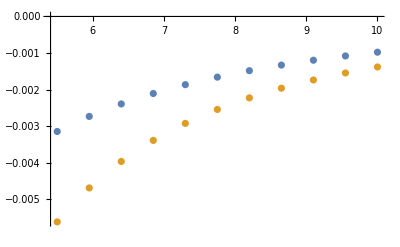

```mathematica
ListPlot[{Lysmallb1, Lysmallb2}]
```

```mathematica
SphericalBesselJ[1,x]
```

SphericalBesselJ[1,x]

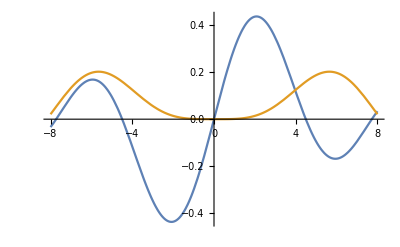

```mathematica
Plot[{SphericalBesselJ[1,x],SphericalBesselJ[4,x]},{x,-8,8}]
```

```mathematica
αlm[4,1]
```

0.189235

```mathematica
162*30
```

4860

```mathematica
16/130.
```

0.123077